# Análisis de las unidades de tiempo

## People= 100, 1000 Capcity= 1,2,3,4,5,6,7,8,9,10 time=1000,10000,100000

```mathematica
SetDirectory[NotebookDirectory[]];
```

## People=100 Capacity=[1-10]

```mathematica
timeVals={1000,10000,100000};
people100=Table[Import[StringJoin["graphs/model-v3/people100/","network-100-",IntegerString[i],"-",IntegerString[timeVals[[j]]],".g6"]],{i,1,10,1},{j,1,3,1}];
```

### Grado de los nodos

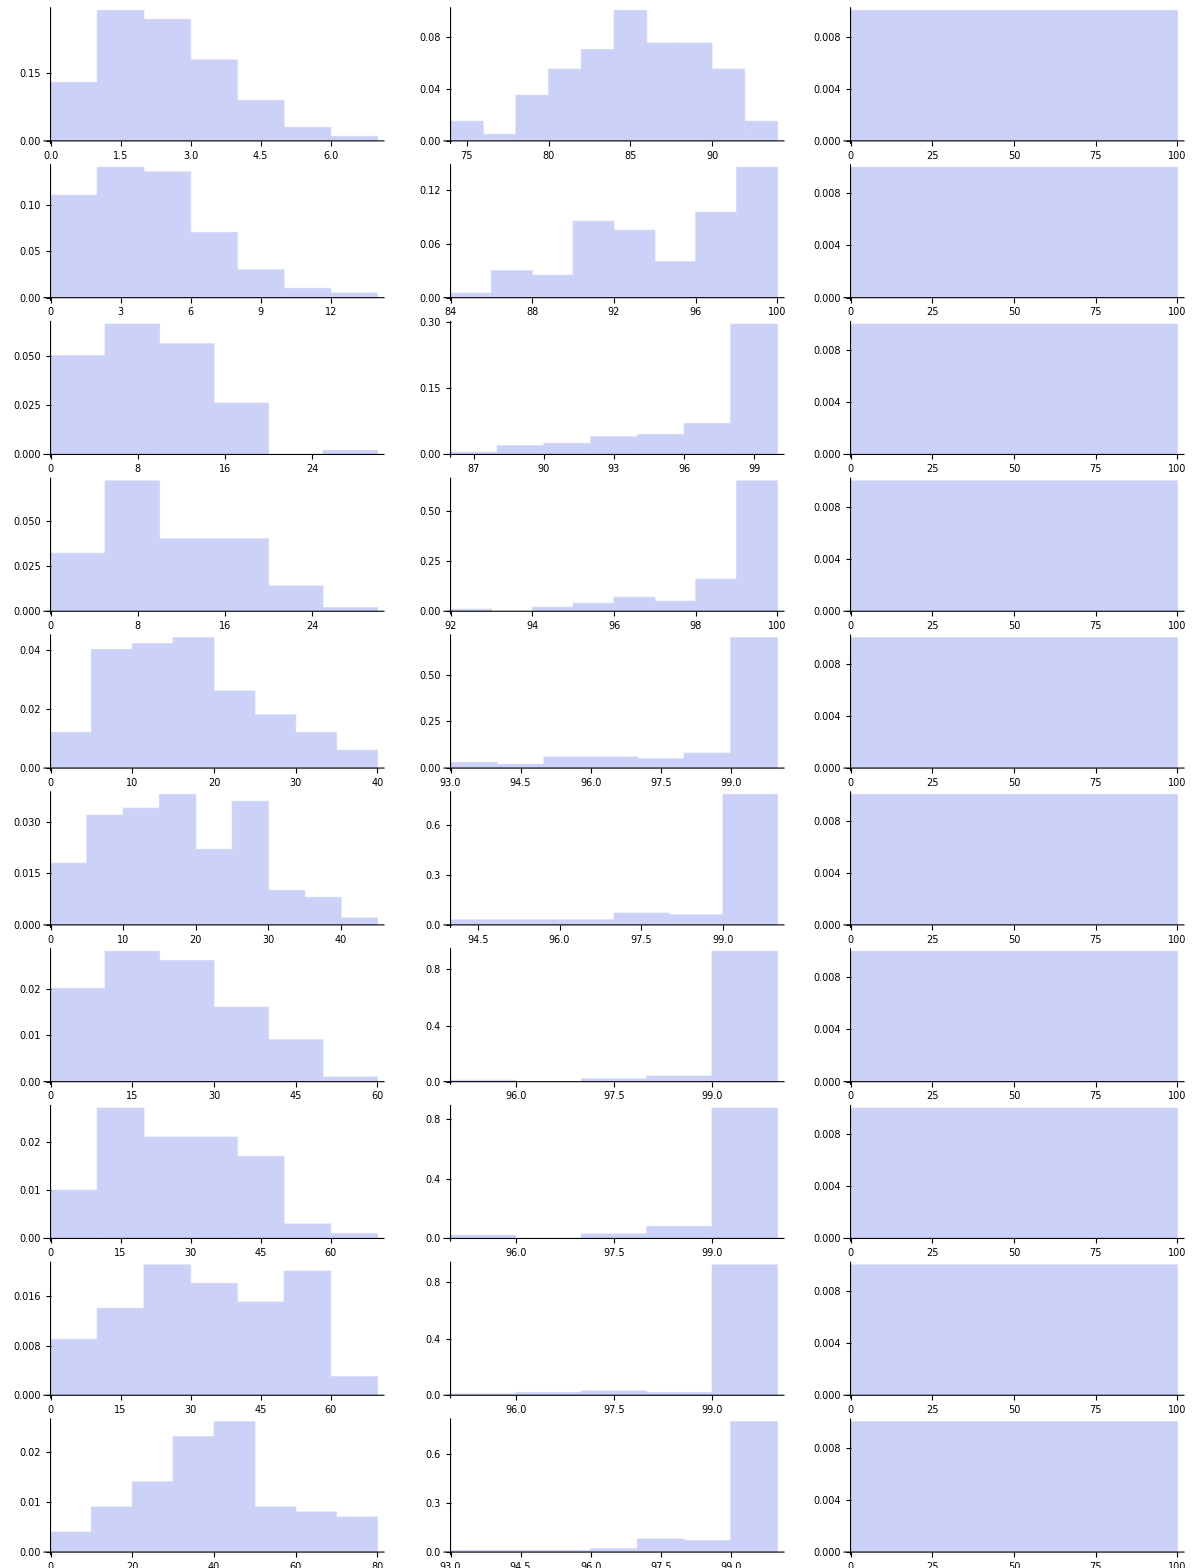

```mathematica
Table[Histogram[VertexDegree[people100[[i,j]]],Automatic,"PDF"],{i,1,Length[people100],1},{j,1,Length[people100[[i]]],1}];
TableForm[%]
```

### Clustering coefficient

```mathematica
clustering100=Map[GlobalClusteringCoefficient,Flatten[people100]];
xy=Table[{i,timeVals[[j]]},{i,1,10,1},{j,1,3,1}];
dataPlotClustering100=Table[Append[Flatten[xy,1][[i]],clustering100[[i]]],{i,1,Length[clustering100],1}];
ListPlot3D[dataPlotClustering100]
```

-Graphics3D-

#### time vs clustering coefficient

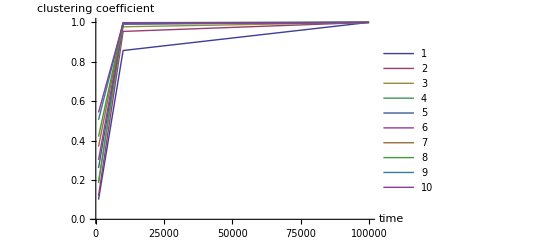

```mathematica
clusteringTime100=Table[Map[GlobalClusteringCoefficient,people100[[i]]],{i,1,Length[people100],1}];
dataPlotClusteringTime100=Table[Table[{timeVals[[j]],clusteringTime100[[i,j]]},{j,1,3,1}],{i,1,10,1}];
ListLinePlot[dataPlotClusteringTime100,PlotLegends->Range[10],AxesLabel->{"time","clustering coefficient"}]
```

#### capacity vs clustering coefficient

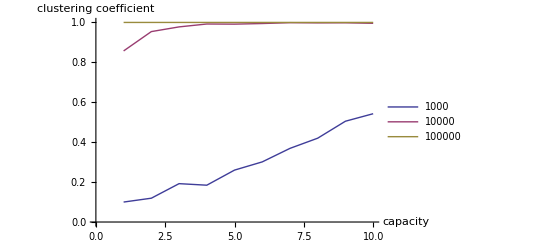

```mathematica
clusteringCap100=Table[Map[GlobalClusteringCoefficient,people100[[i]]],{i,1,Length[people100],1}];
dataPlotClusteringCap100=Table[Table[{i,clusteringTime100[[i,j]]},{i,1,10,1}],{j,1,3,1}];
ListLinePlot[dataPlotClusteringCap100,PlotLegends->timeVals,AxesLabel->{"capacity","clustering coefficient"}]
```

### Average path length

```mathematica
apl100=Map[MeanGraphDistance,Flatten[people100]];
xy=Table[{i,timeVals[[j]]},{i,1,10,1},{j,1,3,1}];
dataPlotApl100=Table[Append[Flatten[xy,1][[i]],apl100[[i]]],{i,1,Length[apl100],1}];
ListPlot3D[dataPlotApl100]
```

-Graphics3D-

#### time vs average path length

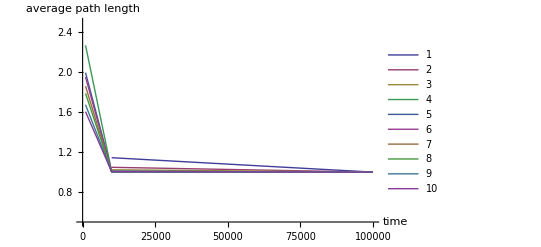

```mathematica
aplTime100=Table[Map[MeanGraphDistance,people100[[i]]],{i,1,Length[people100],1}];
dataPlotAplTime100=Table[Table[{timeVals[[j]],aplTime100[[i,j]]},{j,1,3,1}],{i,1,10,1}];
ListLinePlot[dataPlotAplTime100,PlotLegends->Range[10],AxesLabel->{"time","average path length"},PlotRange->{{0,100000},{0.5,2.5}}]
```

#### capacity vs average path length

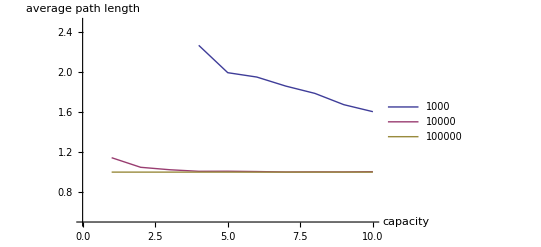

```mathematica
aplCap100=Table[Map[MeanGraphDistance,people100[[i]]],{i,1,Length[people100],1}];
dataPlotAplCap100=Table[Table[{i,aplCap100[[i,j]]},{i,1,10,1}],{j,1,3,1}];
ListLinePlot[dataPlotAplCap100,PlotLegends->timeVals,AxesLabel->{"capacity","average path length"},PlotRange->{{0,10},{0.5,2.5}}]
```

## People=1000 Capacity=[1-10]

```mathematica
timeVals={1000,10000,100000};
people1000=Table[Import[StringJoin["graphs/model-v3/people1000/","network-1000-",IntegerString[i],"-",IntegerString[timeVals[[j]]],".g6"]],{i,1,10,1},{j,1,3,1}];
```

### Grado de los nodos

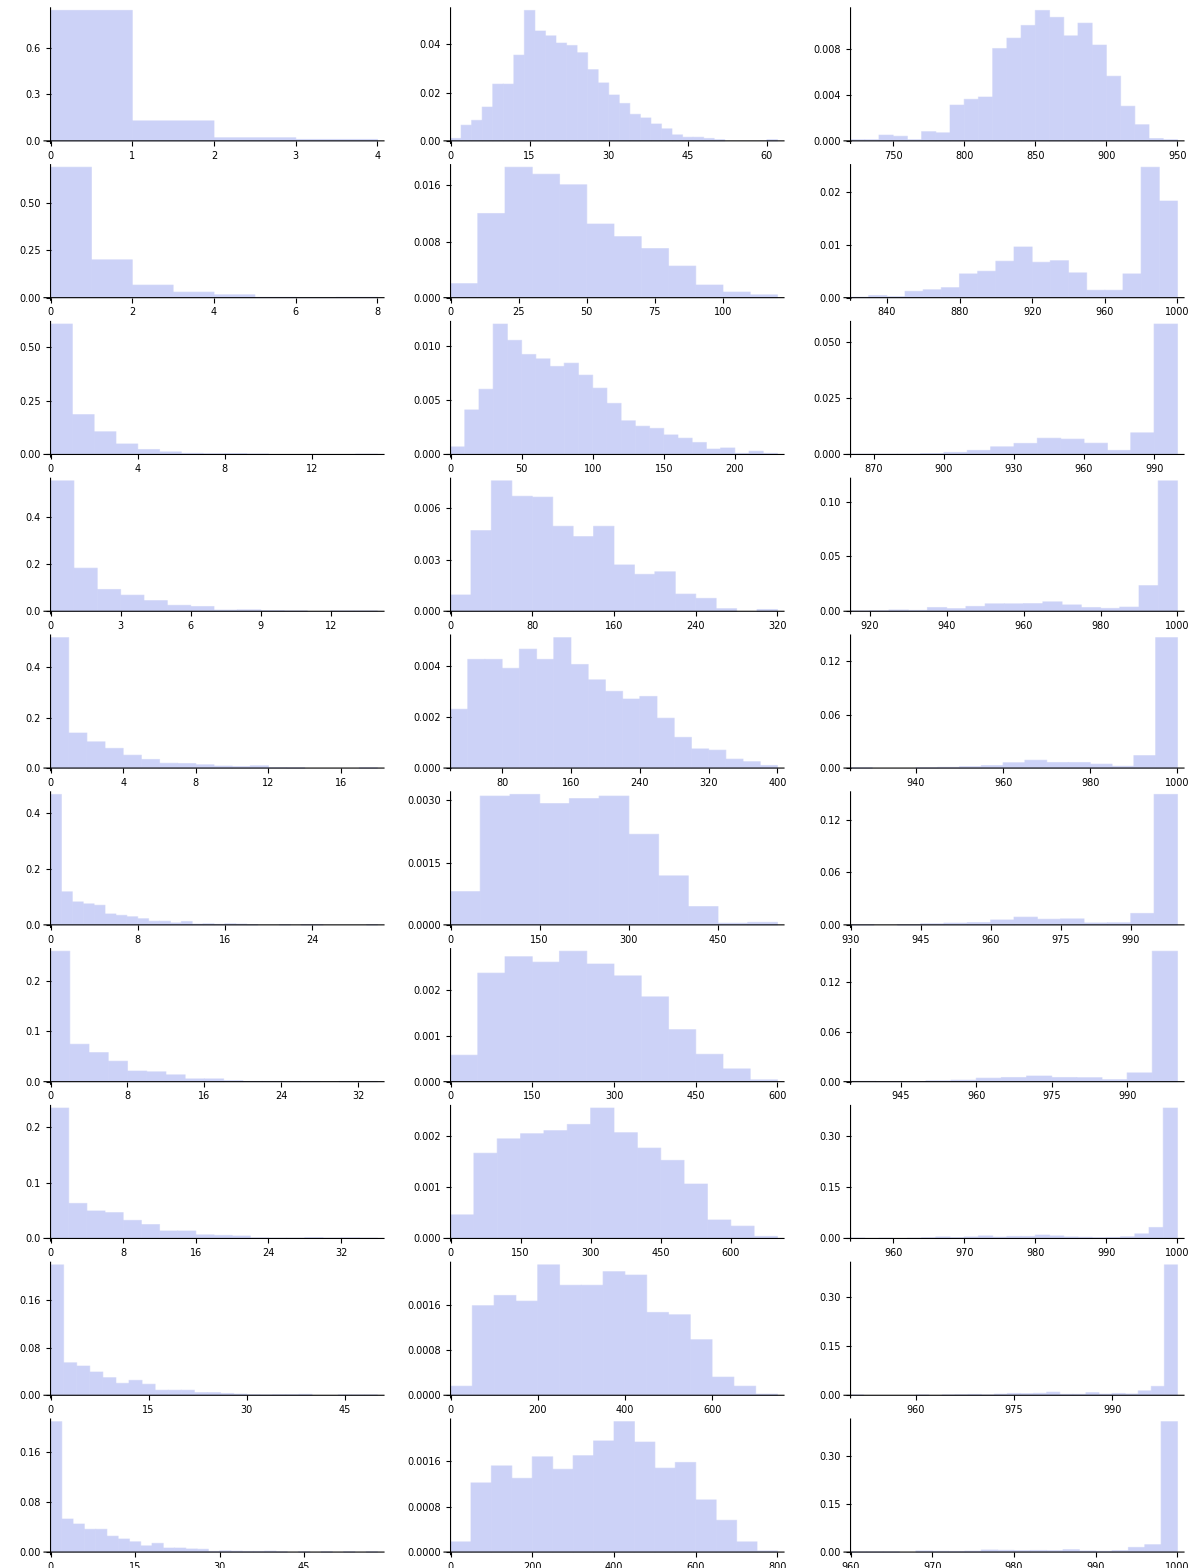

```mathematica
Table[Histogram[VertexDegree[people1000[[i,j]]],Automatic,"PDF"],{i,1,Length[people100],1},{j,1,Length[people100[[i]]],1}];
TableForm[%]
```

### Clustering coefficient

```mathematica
clustering1000=Map[GlobalClusteringCoefficient,Flatten[people1000]];
xy=Table[{i,timeVals[[j]]},{i,1,10,1},{j,1,3,1}];
dataPlotClustering1000=Table[Append[Flatten[xy,1][[i]],clustering1000[[i]]],{i,1,Length[clustering1000],1}];
ListPlot3D[dataPlotClustering1000]
```

-Graphics3D-

#### time vs clustering coefficient

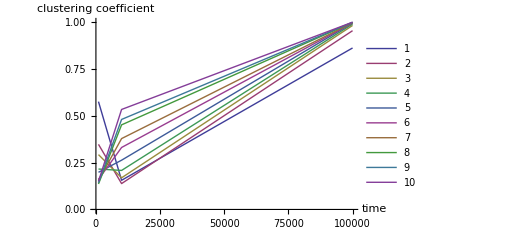

```mathematica
clusteringTime1000=Table[Map[GlobalClusteringCoefficient,people1000[[i]]],{i,1,Length[people1000],1}];
dataPlotClusteringTime1000=Table[Table[{timeVals[[j]],clusteringTime1000[[i,j]]},{j,1,3,1}],{i,1,10,1}];
ListLinePlot[dataPlotClusteringTime1000,PlotLegends->Range[10],AxesLabel->{"time","clustering coefficient"}]
```

#### capacity vs clustering coefficient

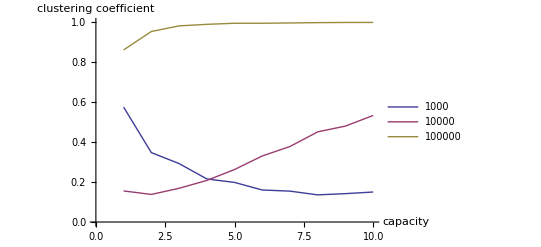

```mathematica
clusteringCap1000=Table[Map[GlobalClusteringCoefficient,people1000[[i]]],{i,1,Length[people1000],1}];
dataPlotClusteringCap1000=Table[Table[{i,clusteringTime1000[[i,j]]},{i,1,10,1}],{j,1,3,1}];
ListLinePlot[dataPlotClusteringCap1000,PlotLegends->timeVals,AxesLabel->{"capacity","clustering coefficient"}]
```

### Average path length

```mathematica
apl1000=Map[MeanGraphDistance,Flatten[people1000]];
xy=Table[{i,timeVals[[j]]},{i,1,10,1},{j,1,3,1}];
dataPlotApl1000=Table[Append[Flatten[xy,1][[i]],apl1000[[i]]],{i,1,Length[apl1000],1}];
ListPlot3D[dataPlotApl1000]
```

-Graphics3D-

#### time vs average path length

{{∞,∞,38041/33300},{∞,182141/83250,19443/18500},{∞,99103/49950,6799/6660},{∞,238783/124875,505697/499500},{∞,231019/124875,502879/499500},{∞,179623/99900,33521/33300},{∞,881053/499500,502051/499500},{∞,71128/41625,6683/6660},{∞,∞,500791/499500},{∞,817339/499500,41723/41625}}

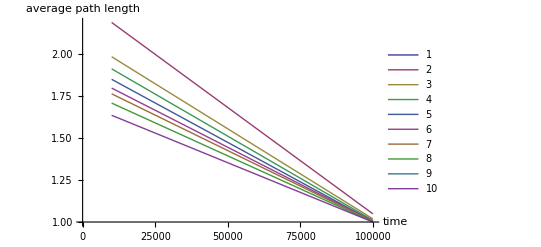

```mathematica
aplTime1000=Table[Map[MeanGraphDistance,people1000[[i]]],{i,1,Length[people1000],1}]
dataPlotAplTime1000=Table[Table[{timeVals[[j]],aplTime1000[[i,j]]},{j,1,3,1}],{i,1,10,1}];
ListLinePlot[dataPlotAplTime1000,PlotLegends->Range[10],AxesLabel->{"time","average path length"}]
```

#### capacity vs average path length

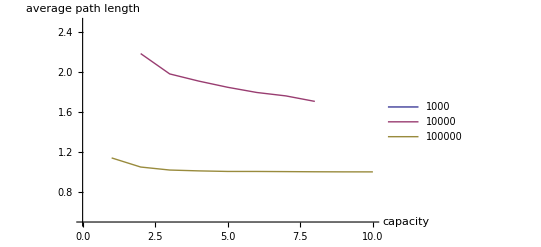

```mathematica
aplCap1000=Table[Map[MeanGraphDistance,people1000[[i]]],{i,1,Length[people1000],1}];
dataPlotAplCap1000=Table[Table[{i,aplCap1000[[i,j]]},{i,1,10,1}],{j,1,3,1}];
ListLinePlot[dataPlotAplCap1000,PlotLegends->timeVals,AxesLabel->{"capacity","average path length"},
PlotRange->{{0,10},{0.5,2.5}}]
```